Existence equations

```mathematica
Integrate[Exp[-s]Sin[nu1 s](1+b Cos[nu2 s]),{s,0,Infinity}]
Integrate[Exp[-s]Sin[nu2 s](1+b Cos[nu1 s]),{s,0,Infinity}]
```

ConditionalExpression[nu1/(1+nu1^2)+1/2 b ((nu1-nu2)/(1+(nu1-nu2)^2)+(nu1+nu2)/(1+(nu1+nu2)^2)),Abs[Im[nu1]]+Abs[Im[nu2]]<1]

ConditionalExpression[nu2/(1+nu2^2)+(b (nu2-nu1^2 nu2+nu2^3))/(nu1^4-2 nu1^2 (-1+nu2^2)+(1+nu2^2)^2),Abs[Im[nu1]]+Abs[Im[nu2]]<1]

Evans function calculations. see log_youngmin2.*

```mathematica
Clear[nu1,nu2,b]
```

```mathematica
(* phat1 *)
Integrate[Exp[-s]Cos[nu1 s](1+b Cos[nu2 s])(Exp[-al s]Cos[-be s]-1),{s,0,Infinity}, Assumptions->{al∈Reals,al>-1,b∈Reals,b≥0,al∈Reals,be∈Reals,nu1∈Reals,nu2∈Reals}]
```

$Aborted

```mathematica
ph1=-1/(1+nu1^2)+((1+al) b (1+6 al^5+al^6+be^6+3 nu1^2+3 nu1^4+nu1^6+3 nu2^2+2 nu1^2 nu2^2-nu1^4 nu2^2+3 nu2^4-nu1^2 nu2^4+nu2^6-be^4 (-3+nu1^2+nu2^2)+3 al^4 (5+be^2+nu1^2+nu2^2)+4 al^3 (5+3 be^2+3 nu1^2+3 nu2^2)+2 al (3 be^4+3 nu1^4+3 (1+nu2^2)^2+2 nu1^2 (3+nu2^2)+2 be^2 (3+nu1^2+nu2^2))-be^2 (-3+nu1^4-2 nu2^2+nu2^4-2 nu1^2 (1+5 nu2^2))+al^2 (3 be^4+3 nu1^4+2 nu1^2 (9+nu2^2)+2 be^2 (9+nu1^2+nu2^2)+3 (5+6 nu2^2+nu2^4))))/((1+2 al+al^2+be^2+nu1^2+2 be (nu1-nu2)-2 nu1 nu2+nu2^2) (1+2 al+al^2+be^2-2 be nu1+nu1^2+2 be nu2-2 nu1 nu2+nu2^2) (1+2 al+al^2+be^2+nu1^2+2 nu1 nu2+nu2^2-2 be (nu1+nu2)) (1+2 al+al^2+be^2+nu1^2+2 nu1 nu2+nu2^2+2 be (nu1+nu2)))+1/2 (((1+al) Cos[2 ArcTan[Abs[be-nu1]/(1+al)]])/((1+al)^2+be^2-2 be nu1+nu1^2)+((1+al) Cos[2 ArcTan[Abs[be+nu1]/(1+al)]])/((1+al)^2+be^2+2 be nu1+nu1^2)+(Abs[be-nu1] Sin[2 ArcTan[Abs[be-nu1]/(1+al)]])/((1+al)^2+be^2-2 be nu1+nu1^2)+(Abs[be+nu1] Sin[2 ArcTan[Abs[be+nu1]/(1+al)]])/((1+al)^2+be^2+2 be nu1+nu1^2))-1/2 b (Cos[2 ArcTan[Abs[nu1-nu2]]]/(1+nu1^2-2 nu1 nu2+nu2^2)+Cos[2 ArcTan[Abs[nu1+nu2]]]/(1+nu1^2+2 nu1 nu2+nu2^2)+(Abs[nu1-nu2] Sin[2 ArcTan[Abs[nu1-nu2]]])/(1+nu1^2-2 nu1 nu2+nu2^2)+(Abs[nu1+nu2] Sin[2 ArcTan[Abs[nu1+nu2]]])/(1+nu1^2+2 nu1 nu2+nu2^2));
```

```mathematica
ph1/.nu1->1.3/.nu2->2.274/.g->3.385/.b->.8/.al-> -.00017/.be->1.2212
```

0.22071

```mathematica
FullSimplify[ph1]
```

$Aborted

```mathematica
FortranForm[ph1]
```

-(1/(1 + nu1**2)) + ((1 + al)*b*(1 + 6*al**5 + al**6 + be**6 + 3*nu1**2 + 3*nu1**4 + nu1**6 + 3*nu2**2 + 
     -       2*nu1**2*nu2**2 - nu1**4*nu2**2 + 3*nu2**4 - nu1**2*nu2**4 + nu2**6 - be**4*(-3 + nu1**2 + nu2**2) + 
     -       3*al**4*(5 + be**2 + nu1**2 + nu2**2) + 4*al**3*(5 + 3*be**2 + 3*nu1**2 + 3*nu2**2) + 
     -       2*al*(3*be**4 + 3*nu1**4 + 3*(1 + nu2**2)**2 + 2*nu1**2*(3 + nu2**2) + 2*be**2*(3 + nu1**2 + nu2**2)) - 
     -       be**2*(-3 + nu1**4 - 2*nu2**2 + nu2**4 - 2*nu1**2*(1 + 5*nu2**2)) + 
     -       al**2*(3*be**4 + 3*nu1**4 + 2*nu1**2*(9 + nu2**2) + 2*be**2*(9 + nu1**2 + nu2**2) + 3*(5 + 6*nu2**2 + nu2**4)))
     -     )/((1 + 2*al + al**2 + be**2 + nu1**2 + 2*be*(nu1 - nu2) - 2*nu1*nu2 + nu2**2)*
     -     (1 + 2*al + al**2 + be**2 - 2*be*nu1 + nu1**2 + 2*be*nu2 - 2*nu1*nu2 + nu2**2)*
     -     (1 + 2*al + al**2 + be**2 + nu1**2 + 2*nu1*nu2 + nu2**2 - 2*be*(nu1 + nu2))*
     -     (1 + 2*al + al**2 + be**2 + nu1**2 + 2*nu1*nu2 + nu2**2 + 2*be*(nu1 + nu2))) + 
     -  (((1 + al)*Cos(2*ArcTan(Abs(be - nu1)/(1 + al))))/((1 + al)**2 + be**2 - 2*be*nu1 + nu1**2) + 
     -     ((1 + al)*Cos(2*ArcTan(Abs(be + nu1)/(1 + al))))/((1 + al)**2 + be**2 + 2*be*nu1 + nu1**2) + 
     -     (Abs(be - nu1)*Sin(2*ArcTan(Abs(be - nu1)/(1 + al))))/((1 + al)**2 + be**2 - 2*be*nu1 + nu1**2) + 
     -     (Abs(be + nu1)*Sin(2*ArcTan(Abs(be + nu1)/(1 + al))))/((1 + al)**2 + be**2 + 2*be*nu1 + nu1**2))/2. - 
     -  (b*(Cos(2*ArcTan(Abs(nu1 - nu2)))/(1 + nu1**2 - 2*nu1*nu2 + nu2**2) + 
     -       Cos(2*ArcTan(Abs(nu1 + nu2)))/(1 + nu1**2 + 2*nu1*nu2 + nu2**2) + 
     -       (Abs(nu1 - nu2)*Sin(2*ArcTan(Abs(nu1 - nu2))))/(1 + nu1**2 - 2*nu1*nu2 + nu2**2) + 
     -       (Abs(nu1 + nu2)*Sin(2*ArcTan(Abs(nu1 + nu2))))/(1 + nu1**2 + 2*nu1*nu2 + nu2**2)))/2.

```mathematica
(* qhat 1 (not Qhat 1) *)
Integrate[Exp[-s]Cos[nu1 s](1+b Cos[nu2 s])Exp[-al s]Sin[-be s],{s,0,Infinity},Assumptions->{a∈Reals,a>-1,b∈Reals,b≥0,al∈Reals,be∈Reals,nu1∈Reals,nu2∈Reals}]
```

ConditionalExpression[-(be ((1+al)^2+be^2-nu1^2))/(be^4-2 be^2 (-(1+al)^2+nu1^2)+((1+al)^2+nu1^2)^2)-(b be (1+6 al^5+al^6+be^6+nu1^2-nu1^4-nu1^6+nu2^2+10 nu1^2 nu2^2+nu1^4 nu2^2-nu2^4+nu1^2 nu2^4-nu2^6-3 be^4 (-1+nu1^2+nu2^2)+4 al^3 (5+3 be^2+nu1^2+nu2^2)+al^4 (15+3 be^2+nu1^2+nu2^2)+be^2 (3+3 nu1^4-2 nu2^2+3 nu2^4+2 nu1^2 (-1+nu2^2))+2 al (3+3 be^4-nu1^4+2 nu2^2-nu2^4-2 be^2 (-3+nu1^2+nu2^2)+2 nu1^2 (1+5 nu2^2))+al^2 (15+3 be^4-nu1^4+6 nu2^2-nu2^4-2 be^2 (-9+nu1^2+nu2^2)+2 nu1^2 (3+5 nu2^2))))/((1+2 al+al^2+be^2+nu1^2+2 be (nu1-nu2)-2 nu1 nu2+nu2^2) (1+2 al+al^2+be^2-2 be nu1+nu1^2+2 be nu2-2 nu1 nu2+nu2^2) (1+2 al+al^2+be^2+nu1^2+2 nu1 nu2+nu2^2-2 be (nu1+nu2)) (1+2 al+al^2+be^2+nu1^2+2 nu1 nu2+nu2^2+2 be (nu1+nu2))),al>-1]

```mathematica
qh1=-(be ((1+al)^2+be^2-nu1^2))/(be^4-2 be^2 (-(1+al)^2+nu1^2)+((1+al)^2+nu1^2)^2)-(b be (1+6 al^5+al^6+be^6+nu1^2-nu1^4-nu1^6+nu2^2+10 nu1^2 nu2^2+nu1^4 nu2^2-nu2^4+nu1^2 nu2^4-nu2^6-3 be^4 (-1+nu1^2+nu2^2)+4 al^3 (5+3 be^2+nu1^2+nu2^2)+al^4 (15+3 be^2+nu1^2+nu2^2)+be^2 (3+3 nu1^4-2 nu2^2+3 nu2^4+2 nu1^2 (-1+nu2^2))+2 al (3+3 be^4-nu1^4+2 nu2^2-nu2^4-2 be^2 (-3+nu1^2+nu2^2)+2 nu1^2 (1+5 nu2^2))+al^2 (15+3 be^4-nu1^4+6 nu2^2-nu2^4-2 be^2 (-9+nu1^2+nu2^2)+2 nu1^2 (3+5 nu2^2))))/((1+2 al+al^2+be^2+nu1^2+2 be (nu1-nu2)-2 nu1 nu2+nu2^2) (1+2 al+al^2+be^2-2 be nu1+nu1^2+2 be nu2-2 nu1 nu2+nu2^2) (1+2 al+al^2+be^2+nu1^2+2 nu1 nu2+nu2^2-2 be (nu1+nu2)) (1+2 al+al^2+be^2+nu1^2+2 nu1 nu2+nu2^2+2 be (nu1+nu2)));
```

```mathematica
FortranForm[qh1]
```

-((be*((1 + al)**2 + be**2 - nu1**2))/(be**4 - 2*be**2*(-(1 + al)**2 + nu1**2) + ((1 + al)**2 + nu1**2)**2)) - 
     -  (b*be*(1 + 6*al**5 + al**6 + be**6 + nu1**2 - nu1**4 - nu1**6 + nu2**2 + 10*nu1**2*nu2**2 + nu1**4*nu2**2 - 
     -       nu2**4 + nu1**2*nu2**4 - nu2**6 - 3*be**4*(-1 + nu1**2 + nu2**2) + 4*al**3*(5 + 3*be**2 + nu1**2 + nu2**2) + 
     -       al**4*(15 + 3*be**2 + nu1**2 + nu2**2) + be**2*(3 + 3*nu1**4 - 2*nu2**2 + 3*nu2**4 + 2*nu1**2*(-1 + nu2**2)) + 
     -       2*al*(3 + 3*be**4 - nu1**4 + 2*nu2**2 - nu2**4 - 2*be**2*(-3 + nu1**2 + nu2**2) + 2*nu1**2*(1 + 5*nu2**2)) + 
     -       al**2*(15 + 3*be**4 - nu1**4 + 6*nu2**2 - nu2**4 - 2*be**2*(-9 + nu1**2 + nu2**2) + 2*nu1**2*(3 + 5*nu2**2))))/
     -   ((1 + 2*al + al**2 + be**2 + nu1**2 + 2*be*(nu1 - nu2) - 2*nu1*nu2 + nu2**2)*
     -     (1 + 2*al + al**2 + be**2 - 2*be*nu1 + nu1**2 + 2*be*nu2 - 2*nu1*nu2 + nu2**2)*
     -     (1 + 2*al + al**2 + be**2 + nu1**2 + 2*nu1*nu2 + nu2**2 - 2*be*(nu1 + nu2))*
     -     (1 + 2*al + al**2 + be**2 + nu1**2 + 2*nu1*nu2 + nu2**2 + 2*be*(nu1 + nu2)))

```mathematica
(* phat 2, qhat 2 *)
```

```mathematica
Integrate[-b Exp[-s]Sin[nu1 s]Sin[nu2 s](Exp[-al s]Cos[-be s]-1),{s,0,Infinity},Assumptions->{a∈Reals,a>-1,b∈Reals,b≥0,al∈Reals,be∈Reals,nu1∈Reals,nu2∈Reals}]
Integrate[-b Exp[-s]Sin[nu1 s]Sin[nu2 s](Exp[-al s]Sin[-be s]),{s,0,Infinity},Assumptions->{a∈Reals,a>-1,b∈Reals,b≥0,al∈Reals,be∈Reals,nu1∈Reals,nu2∈Reals}]
```

ConditionalExpression[1/2 b (-((4 (1+al) nu1 nu2 (1+4 al^3+al^4-3 be^4+2 nu1^2+nu1^4+2 nu2^2-2 nu1^2 nu2^2+nu2^4+2 be^2 (-1+nu1^2+nu2^2)+4 al (1-be^2+nu1^2+nu2^2)+2 al^2 (3-be^2+nu1^2+nu2^2)))/((1+2 al+al^2+be^2+nu1^2+2 be (nu1-nu2)-2 nu1 nu2+nu2^2) (1+2 al+al^2+be^2-2 be nu1+nu1^2+2 be nu2-2 nu1 nu2+nu2^2) (1+2 al+al^2+be^2+nu1^2+2 nu1 nu2+nu2^2-2 be (nu1+nu2)) (1+2 al+al^2+be^2+nu1^2+2 nu1 nu2+nu2^2+2 be (nu1+nu2))))+Cos[2 ArcTan[Abs[nu1-nu2]]]/(1+nu1^2-2 nu1 nu2+nu2^2)-Cos[2 ArcTan[Abs[nu1+nu2]]]/(1+nu1^2+2 nu1 nu2+nu2^2)+(Abs[nu1-nu2] Sin[2 ArcTan[Abs[nu1-nu2]]])/(1+nu1^2-2 nu1 nu2+nu2^2)-(Abs[nu1+nu2] Sin[2 ArcTan[Abs[nu1+nu2]]])/(1+nu1^2+2 nu1 nu2+nu2^2)),al>-1]

ConditionalExpression[(2 b be nu1 nu2 (3+12 al^3+3 al^4-be^4+2 nu1^2+2 nu2^2-(nu1^2-nu2^2)^2+2 be^2 (1+nu1^2+nu2^2)+4 al (3+be^2+nu1^2+nu2^2)+2 al^2 (9+be^2+nu1^2+nu2^2)))/((1+al (2+al)+(be+nu1-nu2)^2) (1+al (2+al)+(be-nu1+nu2)^2) (1+al (2+al)+(-be+nu1+nu2)^2) (1+al (2+al)+(be+nu1+nu2)^2)),al>-1]

```mathematica
ph2=1/2 b (-((4 (1+al) nu1 nu2 (1+4 al^3+al^4-3 be^4+2 nu1^2+nu1^4+2 nu2^2-2 nu1^2 nu2^2+nu2^4+2 be^2 (-1+nu1^2+nu2^2)+4 al (1-be^2+nu1^2+nu2^2)+2 al^2 (3-be^2+nu1^2+nu2^2)))/((1+2 al+al^2+be^2+nu1^2+2 be (nu1-nu2)-2 nu1 nu2+nu2^2) (1+2 al+al^2+be^2-2 be nu1+nu1^2+2 be nu2-2 nu1 nu2+nu2^2) (1+2 al+al^2+be^2+nu1^2+2 nu1 nu2+nu2^2-2 be (nu1+nu2)) (1+2 al+al^2+be^2+nu1^2+2 nu1 nu2+nu2^2+2 be (nu1+nu2))))+Cos[2 ArcTan[Abs[nu1-nu2]]]/(1+nu1^2-2 nu1 nu2+nu2^2)-Cos[2 ArcTan[Abs[nu1+nu2]]]/(1+nu1^2+2 nu1 nu2+nu2^2)+(Abs[nu1-nu2] Sin[2 ArcTan[Abs[nu1-nu2]]])/(1+nu1^2-2 nu1 nu2+nu2^2)-(Abs[nu1+nu2] Sin[2 ArcTan[Abs[nu1+nu2]]])/(1+nu1^2+2 nu1 nu2+nu2^2));
qh2=(2 b be nu1 nu2 (3+12 al^3+3 al^4-be^4+2 nu1^2+2 nu2^2-(nu1^2-nu2^2)^2+2 be^2 (1+nu1^2+nu2^2)+4 al (3+be^2+nu1^2+nu2^2)+2 al^2 (9+be^2+nu1^2+nu2^2)))/((1+al (2+al)+(be+nu1-nu2)^2) (1+al (2+al)+(be-nu1+nu2)^2) (1+al (2+al)+(-be+nu1+nu2)^2) (1+al (2+al)+(be+nu1+nu2)^2));
```

```mathematica
FortranForm[ph2]
```

(b*((-4*(1 + al)*nu1*nu2*(1 + 4*al**3 + al**4 - 3*be**4 + 2*nu1**2 + nu1**4 + 2*nu2**2 - 2*nu1**2*nu2**2 + nu2**4 + 
     -           2*be**2*(-1 + nu1**2 + nu2**2) + 4*al*(1 - be**2 + nu1**2 + nu2**2) + 2*al**2*(3 - be**2 + nu1**2 + nu2**2)
     -           ))/((1 + 2*al + al**2 + be**2 + nu1**2 + 2*be*(nu1 - nu2) - 2*nu1*nu2 + nu2**2)*
     -         (1 + 2*al + al**2 + be**2 - 2*be*nu1 + nu1**2 + 2*be*nu2 - 2*nu1*nu2 + nu2**2)*
     -         (1 + 2*al + al**2 + be**2 + nu1**2 + 2*nu1*nu2 + nu2**2 - 2*be*(nu1 + nu2))*
     -         (1 + 2*al + al**2 + be**2 + nu1**2 + 2*nu1*nu2 + nu2**2 + 2*be*(nu1 + nu2))) + 
     -      Cos(2*ArcTan(Abs(nu1 - nu2)))/(1 + nu1**2 - 2*nu1*nu2 + nu2**2) - 
     -      Cos(2*ArcTan(Abs(nu1 + nu2)))/(1 + nu1**2 + 2*nu1*nu2 + nu2**2) + 
     -      (Abs(nu1 - nu2)*Sin(2*ArcTan(Abs(nu1 - nu2))))/(1 + nu1**2 - 2*nu1*nu2 + nu2**2) - 
     -      (Abs(nu1 + nu2)*Sin(2*ArcTan(Abs(nu1 + nu2))))/(1 + nu1**2 + 2*nu1*nu2 + nu2**2)))/2.

```mathematica
FortranForm[qh2]
```

(2*b*be*nu1*nu2*(3 + 12*al**3 + 3*al**4 - be**4 + 2*nu1**2 + 2*nu2**2 - (nu1**2 - nu2**2)**2 + 
     -      2*be**2*(1 + nu1**2 + nu2**2) + 4*al*(3 + be**2 + nu1**2 + nu2**2) + 2*al**2*(9 + be**2 + nu1**2 + nu2**2)))/
     -  ((1 + al*(2 + al) + (be + nu1 - nu2)**2)*(1 + al*(2 + al) + (be - nu1 + nu2)**2)*
     -    (1 + al*(2 + al) + (-be + nu1 + nu2)**2)*(1 + al*(2 + al) + (be + nu1 + nu2)**2))

(2*b*be*nu1*nu2*(3 + 12*al**3 + 3*al**4 - be**4 + 2*nu1**2 + 2*nu2**2 - (nu1**2 - nu2**2)**2 + 
     -      2*be**2*(1 + nu1**2 + nu2**2) + 4*al*(3 + be**2 + nu1**2 + nu2**2) + 2*al**2*(9 + be**2 + nu1**2 + nu2**2)))/
     -  ((1 + al*(2 + al) + (be + nu1 - nu2)**2)*(1 + al*(2 + al) + (be - nu1 + nu2)**2)*
     -    (1 + al*(2 + al) + (-be + nu1 + nu2)**2)*(1 + al*(2 + al) + (be + nu1 + nu2)**2))

```mathematica
FortranForm[qh2]
```

(2*b*be*nu1*nu2*(3 + 12*al**3 + 3*al**4 - be**4 + 2*nu1**2 + 2*nu2**2 - (nu1**2 - nu2**2)**2 + 
     -      2*be**2*(1 + nu1**2 + nu2**2) + 4*al*(3 + be**2 + nu1**2 + nu2**2) + 2*al**2*(9 + be**2 + nu1**2 + nu2**2)))/
     -  ((1 + al*(2 + al) + (be + nu1 - nu2)**2)*(1 + al*(2 + al) + (be - nu1 + nu2)**2)*
     -    (1 + al*(2 + al) + (-be + nu1 + nu2)**2)*(1 + al*(2 + al) + (be + nu1 + nu2)**2))

```mathematica
ph3=ph2;
qh3=qh2;
```

```mathematica
(* phat 4, qhat 4 *)
Integrate[Exp[-s]Cos[nu2 s](1+b Cos[nu1 s])(Exp[-al s]Cos[-be s]-1),{s,0,Infinity},Assumptions->{a∈Reals,a>-1,b∈Reals,b≥0,al∈Reals,be∈Reals,nu1∈Reals,nu2∈Reals}]
Integrate[Exp[-s]Cos[nu2 s](1+b Cos[-nu1 s])Exp[-al s]Sin[-be s],{s,0,Infinity},Assumptions->{a∈Reals,a>-1,b∈Reals,b≥0,al∈Reals,be∈Reals,nu1∈Reals,nu2∈Reals}]
```

ConditionalExpression[-1/(1+nu2^2)+((1+al) b (1+6 al^5+al^6+be^6+3 nu1^2+3 nu1^4+nu1^6+3 nu2^2+2 nu1^2 nu2^2-nu1^4 nu2^2+3 nu2^4-nu1^2 nu2^4+nu2^6-be^4 (-3+nu1^2+nu2^2)+3 al^4 (5+be^2+nu1^2+nu2^2)+4 al^3 (5+3 be^2+3 nu1^2+3 nu2^2)+2 al (3 be^4+3 nu1^4+3 (1+nu2^2)^2+2 nu1^2 (3+nu2^2)+2 be^2 (3+nu1^2+nu2^2))-be^2 (-3+nu1^4-2 nu2^2+nu2^4-2 nu1^2 (1+5 nu2^2))+al^2 (3 be^4+3 nu1^4+2 nu1^2 (9+nu2^2)+2 be^2 (9+nu1^2+nu2^2)+3 (5+6 nu2^2+nu2^4))))/((1+2 al+al^2+be^2+nu1^2+2 be (nu1-nu2)-2 nu1 nu2+nu2^2) (1+2 al+al^2+be^2-2 be nu1+nu1^2+2 be nu2-2 nu1 nu2+nu2^2) (1+2 al+al^2+be^2+nu1^2+2 nu1 nu2+nu2^2-2 be (nu1+nu2)) (1+2 al+al^2+be^2+nu1^2+2 nu1 nu2+nu2^2+2 be (nu1+nu2)))+1/2 (((1+al) Cos[2 ArcTan[Abs[be-nu2]/(1+al)]])/((1+al)^2+be^2-2 be nu2+nu2^2)+((1+al) Cos[2 ArcTan[Abs[be+nu2]/(1+al)]])/((1+al)^2+be^2+2 be nu2+nu2^2)+(Abs[be-nu2] Sin[2 ArcTan[Abs[be-nu2]/(1+al)]])/((1+al)^2+be^2-2 be nu2+nu2^2)+(Abs[be+nu2] Sin[2 ArcTan[Abs[be+nu2]/(1+al)]])/((1+al)^2+be^2+2 be nu2+nu2^2))-1/2 b (Cos[2 ArcTan[Abs[nu1-nu2]]]/(1+nu1^2-2 nu1 nu2+nu2^2)+Cos[2 ArcTan[Abs[nu1+nu2]]]/(1+nu1^2+2 nu1 nu2+nu2^2)+(Abs[nu1-nu2] Sin[2 ArcTan[Abs[nu1-nu2]]])/(1+nu1^2-2 nu1 nu2+nu2^2)+(Abs[nu1+nu2] Sin[2 ArcTan[Abs[nu1+nu2]]])/(1+nu1^2+2 nu1 nu2+nu2^2)),al>-1]

ConditionalExpression[-(be ((1+al)^2+be^2-nu2^2))/(be^4-2 be^2 (-(1+al)^2+nu2^2)+((1+al)^2+nu2^2)^2)-(b be (1+6 al^5+al^6+be^6+nu1^2-nu1^4-nu1^6+nu2^2+10 nu1^2 nu2^2+nu1^4 nu2^2-nu2^4+nu1^2 nu2^4-nu2^6-3 be^4 (-1+nu1^2+nu2^2)+4 al^3 (5+3 be^2+nu1^2+nu2^2)+al^4 (15+3 be^2+nu1^2+nu2^2)+be^2 (3+3 nu1^4-2 nu2^2+3 nu2^4+2 nu1^2 (-1+nu2^2))+2 al (3+3 be^4-nu1^4+2 nu2^2-nu2^4-2 be^2 (-3+nu1^2+nu2^2)+2 nu1^2 (1+5 nu2^2))+al^2 (15+3 be^4-nu1^4+6 nu2^2-nu2^4-2 be^2 (-9+nu1^2+nu2^2)+2 nu1^2 (3+5 nu2^2))))/((1+2 al+al^2+be^2+nu1^2+2 be (nu1-nu2)-2 nu1 nu2+nu2^2) (1+2 al+al^2+be^2-2 be nu1+nu1^2+2 be nu2-2 nu1 nu2+nu2^2) (1+2 al+al^2+be^2+nu1^2+2 nu1 nu2+nu2^2-2 be (nu1+nu2)) (1+2 al+al^2+be^2+nu1^2+2 nu1 nu2+nu2^2+2 be (nu1+nu2))),al>-1]

```mathematica
ph4=-1/(1+nu2^2)+((1+al) b (1+6 al^5+al^6+be^6+3 nu1^2+3 nu1^4+nu1^6+3 nu2^2+2 nu1^2 nu2^2-nu1^4 nu2^2+3 nu2^4-nu1^2 nu2^4+nu2^6-be^4 (-3+nu1^2+nu2^2)+3 al^4 (5+be^2+nu1^2+nu2^2)+4 al^3 (5+3 be^2+3 nu1^2+3 nu2^2)+2 al (3 be^4+3 nu1^4+3 (1+nu2^2)^2+2 nu1^2 (3+nu2^2)+2 be^2 (3+nu1^2+nu2^2))-be^2 (-3+nu1^4-2 nu2^2+nu2^4-2 nu1^2 (1+5 nu2^2))+al^2 (3 be^4+3 nu1^4+2 nu1^2 (9+nu2^2)+2 be^2 (9+nu1^2+nu2^2)+3 (5+6 nu2^2+nu2^4))))/((1+2 al+al^2+be^2+nu1^2+2 be (nu1-nu2)-2 nu1 nu2+nu2^2) (1+2 al+al^2+be^2-2 be nu1+nu1^2+2 be nu2-2 nu1 nu2+nu2^2) (1+2 al+al^2+be^2+nu1^2+2 nu1 nu2+nu2^2-2 be (nu1+nu2)) (1+2 al+al^2+be^2+nu1^2+2 nu1 nu2+nu2^2+2 be (nu1+nu2)))+1/2 (((1+al) Cos[2 ArcTan[Abs[be-nu2]/(1+al)]])/((1+al)^2+be^2-2 be nu2+nu2^2)+((1+al) Cos[2 ArcTan[Abs[be+nu2]/(1+al)]])/((1+al)^2+be^2+2 be nu2+nu2^2)+(Abs[be-nu2] Sin[2 ArcTan[Abs[be-nu2]/(1+al)]])/((1+al)^2+be^2-2 be nu2+nu2^2)+(Abs[be+nu2] Sin[2 ArcTan[Abs[be+nu2]/(1+al)]])/((1+al)^2+be^2+2 be nu2+nu2^2))-1/2 b (Cos[2 ArcTan[Abs[nu1-nu2]]]/(1+nu1^2-2 nu1 nu2+nu2^2)+Cos[2 ArcTan[Abs[nu1+nu2]]]/(1+nu1^2+2 nu1 nu2+nu2^2)+(Abs[nu1-nu2] Sin[2 ArcTan[Abs[nu1-nu2]]])/(1+nu1^2-2 nu1 nu2+nu2^2)+(Abs[nu1+nu2] Sin[2 ArcTan[Abs[nu1+nu2]]])/(1+nu1^2+2 nu1 nu2+nu2^2));
qh4=-(be ((1+al)^2+be^2-nu2^2))/(be^4-2 be^2 (-(1+al)^2+nu2^2)+((1+al)^2+nu2^2)^2)-(b be (1+6 al^5+al^6+be^6+nu1^2-nu1^4-nu1^6+nu2^2+10 nu1^2 nu2^2+nu1^4 nu2^2-nu2^4+nu1^2 nu2^4-nu2^6-3 be^4 (-1+nu1^2+nu2^2)+4 al^3 (5+3 be^2+nu1^2+nu2^2)+al^4 (15+3 be^2+nu1^2+nu2^2)+be^2 (3+3 nu1^4-2 nu2^2+3 nu2^4+2 nu1^2 (-1+nu2^2))+2 al (3+3 be^4-nu1^4+2 nu2^2-nu2^4-2 be^2 (-3+nu1^2+nu2^2)+2 nu1^2 (1+5 nu2^2))+al^2 (15+3 be^4-nu1^4+6 nu2^2-nu2^4-2 be^2 (-9+nu1^2+nu2^2)+2 nu1^2 (3+5 nu2^2))))/((1+2 al+al^2+be^2+nu1^2+2 be (nu1-nu2)-2 nu1 nu2+nu2^2) (1+2 al+al^2+be^2-2 be nu1+nu1^2+2 be nu2-2 nu1 nu2+nu2^2) (1+2 al+al^2+be^2+nu1^2+2 nu1 nu2+nu2^2-2 be (nu1+nu2)) (1+2 al+al^2+be^2+nu1^2+2 nu1 nu2+nu2^2+2 be (nu1+nu2)));
```

```mathematica
FortranForm[ph4]
```

-(1/(1 + nu2**2)) + ((1 + al)*b*(1 + 6*al**5 + al**6 + be**6 + 3*nu1**2 + 3*nu1**4 + nu1**6 + 3*nu2**2 + 
     -       2*nu1**2*nu2**2 - nu1**4*nu2**2 + 3*nu2**4 - nu1**2*nu2**4 + nu2**6 - be**4*(-3 + nu1**2 + nu2**2) + 
     -       3*al**4*(5 + be**2 + nu1**2 + nu2**2) + 4*al**3*(5 + 3*be**2 + 3*nu1**2 + 3*nu2**2) + 
     -       2*al*(3*be**4 + 3*nu1**4 + 3*(1 + nu2**2)**2 + 2*nu1**2*(3 + nu2**2) + 2*be**2*(3 + nu1**2 + nu2**2)) - 
     -       be**2*(-3 + nu1**4 - 2*nu2**2 + nu2**4 - 2*nu1**2*(1 + 5*nu2**2)) + 
     -       al**2*(3*be**4 + 3*nu1**4 + 2*nu1**2*(9 + nu2**2) + 2*be**2*(9 + nu1**2 + nu2**2) + 3*(5 + 6*nu2**2 + nu2**4)))
     -     )/((1 + 2*al + al**2 + be**2 + nu1**2 + 2*be*(nu1 - nu2) - 2*nu1*nu2 + nu2**2)*
     -     (1 + 2*al + al**2 + be**2 - 2*be*nu1 + nu1**2 + 2*be*nu2 - 2*nu1*nu2 + nu2**2)*
     -     (1 + 2*al + al**2 + be**2 + nu1**2 + 2*nu1*nu2 + nu2**2 - 2*be*(nu1 + nu2))*
     -     (1 + 2*al + al**2 + be**2 + nu1**2 + 2*nu1*nu2 + nu2**2 + 2*be*(nu1 + nu2))) + 
     -  (((1 + al)*Cos(2*ArcTan(Abs(be - nu2)/(1 + al))))/((1 + al)**2 + be**2 - 2*be*nu2 + nu2**2) + 
     -     ((1 + al)*Cos(2*ArcTan(Abs(be + nu2)/(1 + al))))/((1 + al)**2 + be**2 + 2*be*nu2 + nu2**2) + 
     -     (Abs(be - nu2)*Sin(2*ArcTan(Abs(be - nu2)/(1 + al))))/((1 + al)**2 + be**2 - 2*be*nu2 + nu2**2) + 
     -     (Abs(be + nu2)*Sin(2*ArcTan(Abs(be + nu2)/(1 + al))))/((1 + al)**2 + be**2 + 2*be*nu2 + nu2**2))/2. - 
     -  (b*(Cos(2*ArcTan(Abs(nu1 - nu2)))/(1 + nu1**2 - 2*nu1*nu2 + nu2**2) + 
     -       Cos(2*ArcTan(Abs(nu1 + nu2)))/(1 + nu1**2 + 2*nu1*nu2 + nu2**2) + 
     -       (Abs(nu1 - nu2)*Sin(2*ArcTan(Abs(nu1 - nu2))))/(1 + nu1**2 - 2*nu1*nu2 + nu2**2) + 
     -       (Abs(nu1 + nu2)*Sin(2*ArcTan(Abs(nu1 + nu2))))/(1 + nu1**2 + 2*nu1*nu2 + nu2**2)))/2.

```mathematica
FortranForm[qh4]
```

-((be*((1 + al)**2 + be**2 - nu2**2))/(be**4 - 2*be**2*(-(1 + al)**2 + nu2**2) + ((1 + al)**2 + nu2**2)**2)) - 
     -  (b*be*(1 + 6*al**5 + al**6 + be**6 + nu1**2 - nu1**4 - nu1**6 + nu2**2 + 10*nu1**2*nu2**2 + nu1**4*nu2**2 - 
     -       nu2**4 + nu1**2*nu2**4 - nu2**6 - 3*be**4*(-1 + nu1**2 + nu2**2) + 4*al**3*(5 + 3*be**2 + nu1**2 + nu2**2) + 
     -       al**4*(15 + 3*be**2 + nu1**2 + nu2**2) + be**2*(3 + 3*nu1**4 - 2*nu2**2 + 3*nu2**4 + 2*nu1**2*(-1 + nu2**2)) + 
     -       2*al*(3 + 3*be**4 - nu1**4 + 2*nu2**2 - nu2**4 - 2*be**2*(-3 + nu1**2 + nu2**2) + 2*nu1**2*(1 + 5*nu2**2)) + 
     -       al**2*(15 + 3*be**4 - nu1**4 + 6*nu2**2 - nu2**4 - 2*be**2*(-9 + nu1**2 + nu2**2) + 2*nu1**2*(3 + 5*nu2**2))))/
     -   ((1 + 2*al + al**2 + be**2 + nu1**2 + 2*be*(nu1 - nu2) - 2*nu1*nu2 + nu2**2)*
     -     (1 + 2*al + al**2 + be**2 - 2*be*nu1 + nu1**2 + 2*be*nu2 - 2*nu1*nu2 + nu2**2)*
     -     (1 + 2*al + al**2 + be**2 + nu1**2 + 2*nu1*nu2 + nu2**2 - 2*be*(nu1 + nu2))*
     -     (1 + 2*al + al**2 + be**2 + nu1**2 + 2*nu1*nu2 + nu2**2 + 2*be*(nu1 + nu2)))

```mathematica
nu1=1.307541;
nu2=2.274371;
g=3.385;
b=.8;
(*Clear[nu1,nu2,g,b,ph1,ph2,ph3,ph4,qh1,qh2,qh3,qh4]*)
ere=g^2(ph1 ph4-qh1 qh4 -ph2 ph3 + qh2 qh3) + g(al(ph1+ph4)-be(qh1+qh4)) + al^2-be^2;
eim=g^2(ph1 qh4+qh1 ph4 - qh2 ph3 - ph2 qh3) + g(al(qh1+qh4)+ be(ph1+ph4))+2al be;
```

```mathematica
FortranForm[ere]
```

al**2 - be**2 + g**2*(-(ph2*ph3) + ph1*ph4 + qh2*qh3 - qh1*qh4) + g*(al*(ph1 + ph4) - be*(qh1 + qh4))

```mathematica
FortranForm[eim]
```

2*al*be + g**2*(ph4*qh1 - ph3*qh2 - ph2*qh3 + ph1*qh4) + g*(be*(ph1 + ph4) + al*(qh1 + qh4))

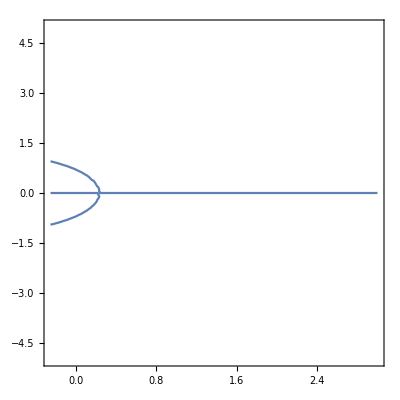

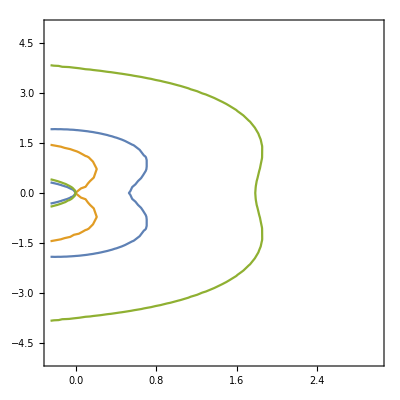

```mathematica
(*ContourPlot[{ere==0,eim==0},{al,-.25,.5},{be,-5,5}]*)
ContourPlot[{qh1==0},{al,-.25,3},{be,-5,5}]
ContourPlot[{ph1==0,ph2==0,ph4==0},{al,-.25,3},{be,-5,5}]
```